```mathematica
Massa:1.50,1.23,1.30,1.30,1.30 (masse solari)
Luminosita':0.722,0.734,0.695,0.831,1.583(rispetto alla luminosita' del Sole)
Temperatura effettiva:3.72,3.71,3.74,3.69,3.67
[Fe/H]:0,0,0,0,0;
```

```mathematica
N[Log10[4.401*10^9]]
```

9.64355

```mathematica
10^9.46
```

2.88403×10^9

```mathematica
BigTab=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\VariousModels\\Practice_Model\\BIGTAB1300.DAT","Table"];
BigTab=Drop[BigTab,400];
BigTab=Drop[BigTab,0];
```

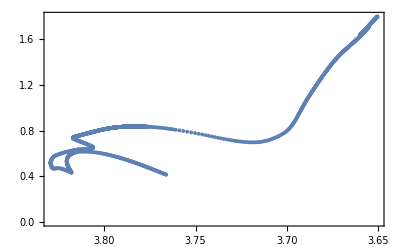

```mathematica
LogTLogL=BigTab[[All,{5,4}]];
ListPlot[LogTLogL,ScalingFunctions->{"Reverse",Identity},Frame->True]
```

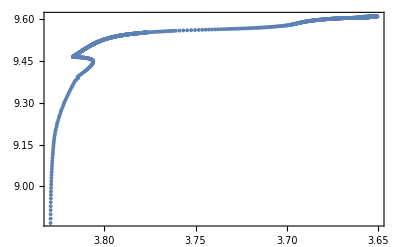

```mathematica
LogTLogAge=BigTab[[All,{5,2}]];
ListPlot[LogTLogAge,ScalingFunctions->{"Reverse",Identity},Frame->True]
```